```mathematica
NestList[Replace[{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}],{1,0,0,1,0},10]//Column
```

{1,0,0,1,0}
{1,0,1,1,0,1}
{1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1}
{0,1,1,1,0,1,1,1,0,1}
{1,0,1,1,1,0,1,0,0}
{1,1,0,1,0,0,1,1,0,1}
{1,0,0,1,1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1,1,1,0,1}

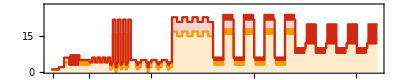

```mathematica
With[{list=Catenate[Table[Tuples[{0,1},n],{n,7}]]},ListStepPlot[Transpose[((Length/@FindTransientRepeat[ResourceFunction["TagSystemEvolveList"]["Post",#,1000],4])&/@list)],Center,PlotRange->{0,28},PlotStyle->{Hue[0.1,1,1],Hue[0.02,0.92,0.8200000000000001]},PlotLayout->"Stacked",Joined->True,Filling->Automatic,Frame->True,AspectRatio->1/5,FrameTicks->{{Automatic,None},{Extract[MapThread[List[#1,Rotate[Style[StringJoin[ToString/@#2],FontFamily->"Roboto",Small],90 Degree]]&,{Range[0,253],list}],Position[list,Alternatives@@Select[list,IntegerExponent[FromDigits[#,2],2]>Length[#]/2&&Length[#]>1&]]],None}}]]
```

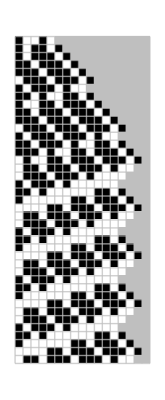
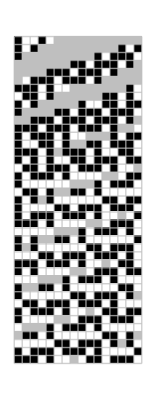

```mathematica
MapIndexed[With[{func=#1,ind=#2},ArrayPlot[MapIndexed[func,PadRight[ResourceFunction["TagSystemEvolveList"]["Post",{1,0,0,1,0},40],If[First[ind]==1,{Automatic,17},Automatic],.25]],Mesh->True,MeshStyle->GrayLevel[0.75,0.75],Frame->False,ImageSize->{Automatic,240}]]&,{#&,RotateLeft[#,3 (First[#2]-1)]&}]
```

```mathematica
Style[Text[Column[Row/@NestList[Replace[#,{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}]&,IntegerDigits[5,2,3],10],Spacings->.2]],FontFamily->"Roboto"]
```

101
1101
11101
011101
10100
001101
10100
001101
10100
001101
10100

```mathematica
TSDirectEvolveSequence[init_,t_]:=First[NestWhile[{Join[First[#],{{0,0},{1,1,0,1}}[[1+#[[1]][[#[[2]]]]]]],#[[2]]+3}&,{init,1},Length[First[#]]>=#[[2]]&,1,t]]
Style[StringJoin[ToString/@TSDirectEvolveSequence[{1,0,1},440]],FontFamily->"Roboto",9]
```

10111011101110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100110100

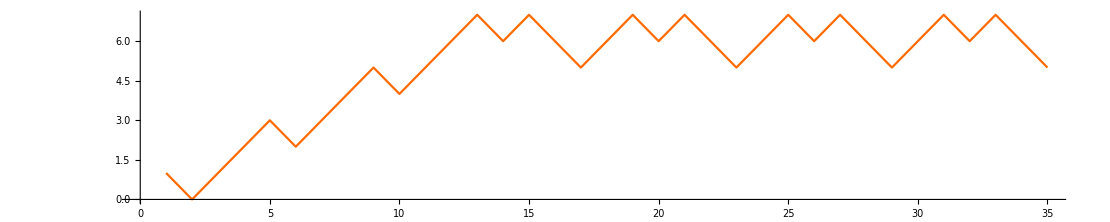

```mathematica
TSDirectEvolveSequence[init_,t_]:=First[
NestWhile[
{Join[
First[#],
{{0,0},{1,1,0,1}}[[1+#[[1]][[#[[2]]]]]]
],
#[[2]]+3}&,
{init,1},
Length[First[#]]>=#[[2]]&,
1,
t
]
]

ListLinePlot[
Accumulate[2 TSDirectEvolveSequence[{1,0,1},10]-1],
AspectRatio->7/35,
PlotStyle->Hue[0.07,1,1]
]
```

```mathematica
CloudGet["https://www.wolframcloud.com/obj/sw-blog/PostTagSystem/Programs-01.wl"];
Style[Text[Column[Row/@NestList[Join[Drop[#,3],{{0,0},{1,1,0,1}}[[1+First[#]]]]&,{0,_,_,1,_,_,1,_,_,1,_,_,1,_,_},10]]],FontFamily->"Roboto"]
```

0__1__1__1__1__
1__1__1__1__00
1__1__1__001101
1__1__0011011101
1__00110111011101
001101110111011101
10111011101110100
110111011101001101
1110111010011011101
01110100110111011101
1010011011101110100

```mathematica
PhasedStringForm[{p_Integer,s_List}]:=Row[{Row[s],Style[Row[{Style[":",Gray],p}],Small]}]

EnumerateInits[n_]:=Catenate[Table[{p,IntegerDigits[i,2,n]},{i,0,2^n-1},{p,0,2}]]

Grid[Transpose@Partition[Text[Style[#,FontFamily->"Roboto"]]&/@PhasedStringForm/@EnumerateInits[3],6],Spacings->{1.5,.2}]
```

000:0 | 010:0 | 100:0 | 110:0
000:1 | 010:1 | 100:1 | 110:1
000:2 | 010:2 | 100:2 | 110:2
001:0 | 011:0 | 101:0 | 111:0
001:1 | 011:1 | 101:1 | 111:1
001:2 | 011:2 | 101:2 | 111:2

```mathematica
NestList[Replace[
{
{0,{0,s___}}->{2,{s,0}},
{0,{1,s___}}->{1,{s,1,1}},
{1,{0,s___}}->{0,{s}},
{1,{1,s___}}->{2,{s,0}},
{2,{0,s___}}->{1,{s,0}},
{2,{1,s___}}->{0,{s,1}}
}
], {1,0,0,1,0},10] //Column
```

{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}
{1,0,0,1,0}

```mathematica
Style[Text[Column[Row/@ResourceFunction["TagSystemEvolveList"]["Post",{1,_,_,0,_},3]]],FontFamily->"Roboto"]
```

1__0_
0_1101
10100
001101

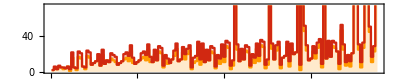

```mathematica
DistinctInits[n_]:=First/@GatherBy[Catenate[Table[Tuples[{0,1},3 n+p],{p,0,2}]],ResourceFunction["TagSystemConvert"][#]&]

ListStepPlot[Transpose[((Length/@FindTransientRepeat[ResourceFunction["TagSystemEvolveList"]["Post",#,1000],4])&/@Catenate[Table[DistinctInits[i],{i,4}]])],Center,PlotRange->{0,Automatic},PlotLayout->"Stacked",PlotStyle->{Hue[0.1,1,1],Hue[0.02,0.92,0.8200000000000001]},Joined->True,Filling->Automatic,Frame->True,AspectRatio->1/5]
```

```mathematica
Replace[{2,011}]
```

Replace[{2,11}]

```mathematica
Style[Text[Column[Row/@ResourceFunction["TagSystemEvolveList"]["Post",{1,_,_,0,_},3]]],FontFamily->"Roboto"]
```

1__0_
0_1101
10100
001101

```mathematica
DistinctInits[n_]:=First/@GatherBy[Catenate[Table[Tuples[{0,1},3 n+p],{p,0,2}]],ResourceFunction["TagSystemConvert"][#]&]

ListStepPlot[Transpose[((Length/@FindTransientRepeat[ResourceFunction["TagSystemEvolveList"]["Post",#,1000],4])&/@Catenate[Table[DistinctInits[i],{i,4}]])],Center,PlotRange->{0,Automatic},PlotLayout->"Stacked",PlotStyle->{Hue[0.1,1,1],Hue[0.02,0.92,0.8200000000000001]},Joined->True,Filling->Automatic,Frame->True,AspectRatio->1/5]
```

-Graphics-

```mathematica
Replace[{
{0,_,_,s___}->{s,0,0},
{1,_,_,s___}->{s,1,1,0,1}
}]
```

Replace[{{0,_,_,s___}→{{2,11},0,0},{1,_,_,s___}→{{2,11},1,1,0,1}}]

```mathematica
NestList[
Replace[{{0,_,_,s___}->{s,0,0},{1,_,_,s___}->{s,1,1,0,1}}],
{1,0,0,1,0},10]//Column
```

{1,0,0,1,0}
{1,0,1,1,0,1}
{1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1}
{0,1,1,1,0,1,1,1,0,1}
{1,0,1,1,1,0,1,0,0}
{1,1,0,1,0,0,1,1,0,1}
{1,0,0,1,1,0,1,1,1,0,1}
{1,1,0,1,1,1,0,1,1,1,0,1}
{1,1,1,0,1,1,1,0,1,1,1,0,1}

```mathematica
NestList[
Replace[{{0,{0,s___}}->{2,{s,0}},{0,{1,s___}}->{1,{s,1,1}},{1,{0,s___}}->{0,{s}},{1,{1,s___}}->{2,{s,0}},{2,{0,s___}}->{1,{s,0}},{2,{1,s___}}->{0,{s,1}}}],
{2,{1,1}},50]//Column
```

{2,{1,1}}
{0,{1,1}}
{1,{1,1,1}}
{2,{1,1,0}}
{0,{1,0,1}}
{1,{0,1,1,1}}
{0,{1,1,1}}
{1,{1,1,1,1}}
{2,{1,1,1,0}}
{0,{1,1,0,1}}
{1,{1,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}
{1,{0,0,0,1,1,1}}
{0,{0,0,1,1,1}}
{2,{0,1,1,1,0}}
{1,{1,1,1,0,0}}
{2,{1,1,0,0,0}}
{0,{1,0,0,0,1}}

```mathematica
DivisorSum[n,k|->EulerPhi[k] 2^(n/k)]/n
```

(∑_(n∣n) 2^(n/n) EulerPhi[n])/n

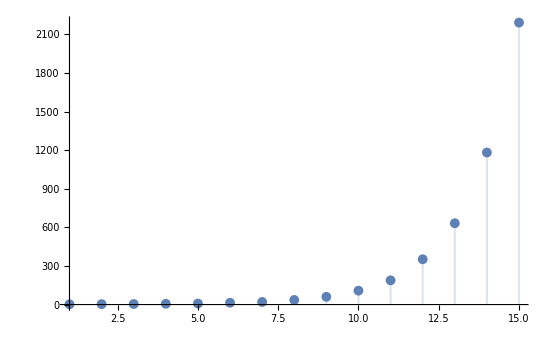

```mathematica
DiscretePlot[DivisorSum[n,k|->EulerPhi[k] 2^(n/k)]/n,{n,15}]
```

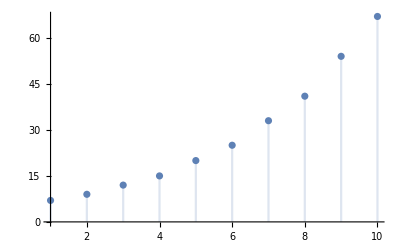

```mathematica
DiscretePlot[∑_i^m Fibonacci[Ceiling[i/2+2]] + 5 ,{m,10}]
```

```mathematica
DiscretePlot[If[EvenQ[m], 2 Fibonacci[m/2 + 4], Fibonacci[(m + 11)/2]] - 1,{m,10}]
```

-Graphics-

```mathematica
Exp[1]
```

ⅇ

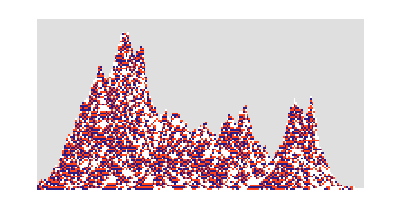

```mathematica
ArrayPlot[Reverse@Transpose[PadRight[Last[ResourceFunction["TagSystemConvert"][#,2]]&/@NestList[Last[ResourceFunction["TagSystemEvolve"][{{0,_,s___}:>{s,0},{1,_,s___}:>{s,0,2},{2,_,s___}:>{s,2,1,1}},#,Quotient[Length[#],2]]]&,IntegerDigits[546,3,6],180],{Automatic,95},.25]],Frame->False,ColorRules->{0->White,1->Hue[.03,.9,1],2->Hue[.7,.8,.5],-1->GrayLevel[.85]}]
```